

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Norm@{x,f[x]}
```

√(Abs[x]^2+Abs[f[x]]^2)

```mathematica
FullSimplify[Norm@{x,f[x]},{x,f[x]}∈Reals]
```

√(x^2+f[x]^2)

```mathematica
D[x^2,{x,-2}]
```

D::dvar: Multiple derivative specifier {x,-2} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,-2} x^2

```mathematica
D[x^2,{x,2}]
```

2

```mathematica
D[x^n,{x,n}]==n
```

(Piecewise[{{FactorialPower[n,n], n≥1}, {x^n, True}}])==n

```mathematica
FullSimplify[D[x^n,{x,n}]==n,n∈]
```

n==n!

```mathematica
FullSimplify[D[x^n,{x,n}],n∈]
```

n!

```mathematica
ArcCurvature[{x,x^3-x^2},x]
```

(2 Abs[-1+3 x])/((1+4 x^2-12 x^3+9 x^4)^(3/2))

```mathematica
FullSimplify[ArcCurvature[{x,x^3-x^2},x],x∈Reals]
```

(2 Abs[1-3 x])/((1+(2-3 x)^2 x^2)^(3/2))

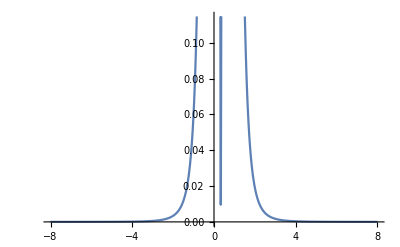

```mathematica
Plot[(2 Abs[1-3 x])/((1+(2-3 x)^2 x^2)^(3/2)),{x,-8,8}]
```

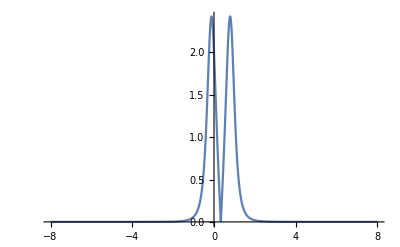

```mathematica
Plot[(2 Abs[1-3 x])/((1+(2-3 x)^2 x^2)^(3/2)),{x,-8,8},PlotRange->Full]
```

```mathematica
Limit[Integrate[ArcCurvature[{x,x^2},x],{x,-a,a}],a->∞]
```

2

```mathematica
Limit[Integrate[ArcCurvature[{x,x^3},x],{x,-a,a}],a->∞]
```

2

```mathematica
Limit[Integrate[ArcCurvature[{x,x^4},x],{x,-a,a}],a->∞]
```

2

```mathematica
Limit[Integrate[ArcCurvature[{x,x^5},x],{x,-a,a}],a->∞]
```

2

```mathematica
Limit[Integrate[ArcCurvature[{x,x},x],{x,-a,a}],a->∞]
```

0

```mathematica
Limit[Integrate[ArcCurvature[{x,x^3-x},x],{x,-a,a}],a->∞]
```

2+√2

```mathematica
Limit[Integrate[ArcCurvature[{x,x^3-x+x^2},x],{x,-a,a}],a->∞]
```

Undefined

```mathematica
Manipulate[
Integrate[ArcCurvature[{x,x^3-x+x^2},x],{x,-a,a}]
,{a,0,100}]
```

```mathematica
1
```

1

```mathematica
1+2+3+4+5
```

15

```mathematica
FullSimplify[ArcCurvature[{x,(x^3-x)/x^a},x],x∈Reals∧a∈]
```

√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3))

```mathematica
2+4
```